```mathematica
phi[t_]:=(ⅇ^(-t^2/4))/(2π)^(1/4)
```

```mathematica
HOM[τ_]:=FullSimplify[1/2-1/2 Abs[Integrate[phi[t]phi[t-τ],{t,-∞,∞}]],{τ∈Reals}]
```

```mathematica
HOM[τ]
```

1/2-1/2 ⅇ^(-τ^2/8)

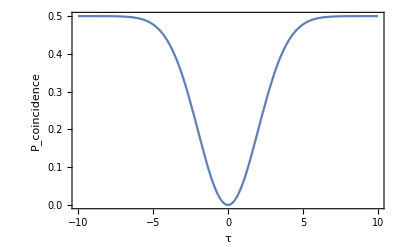

```mathematica
Plot[1/2-1/2 ⅇ^(-τ^2/8),{τ,-10,10},Frame->True,FrameLabel->{"τ","P_coincidence"},LabelStyle->{FontSize->15}]
```